```mathematica
Clear[m,n]
```

```mathematica
$Assumptions={m,n}∈PositiveIntegers;
```

```mathematica
∏_(k=0)^Min[m-1,n-1] (Max[n,m]-k)
```

(Max[m,n]-Min[-1+m,-1+n]) Pochhammer[1+Max[m,n]-Min[-1+m,-1+n],Min[-1+m,-1+n]]

```mathematica
FullSimplify[%]/.{Gamma[q_]->(q-1)!}
```

(Max[m,n]!)/((-1+Max[m,n]-Min[-1+m,-1+n])!)

### Experiment

```mathematica
n=5;
m=5;
p=Range[n];
o=Range[m];
w=RandomVariate[PoissonDistribution[10],n];
pZ=RandomVariate[NormalDistribution[0,10],n];
oZ=RandomVariate[NormalDistribution[0,10],m];
dis=5Ramp[DistanceMatrix[pZ,oZ]-5];
```

```mathematica
f[{p_,o_}]:=dis[[p,o]]
Life[alloc_]:=Total[f/@alloc]
Wait[p_,alloc_]:=Total[w⟦Complement[p,RandomAlloc[p,o][[All,1]]]⟧]
Goal[p_,alloc_]:=Wait[p,alloc]+Life[alloc]
NormlizedGoal[p_,alloc_]:=Goal[p,alloc]-Total[w[[p]]]
RandomAlloc[p_,o_]:=MapIndexed[If[#2[[1]]<=w[[#1[[1]]]]&&f[#1]>w[[#2[[1]]]],#1,Nothing]&,{RandomSample[p][[;;Min[m,n]]],RandomSample[o][[;;Min[m,n]]]}ᵀ]
SampleGoal[p,o]:={NormlizedGoal[p,#], #}&@RandomAlloc[p,o]
```

```mathematica
smps=Table[{#[[1]]/n, #[[2]]}& @SampleGoal[p,o],10000];
scores = #[[1]]&/@smps;
allocations = #[[2]] &/@smps;
```

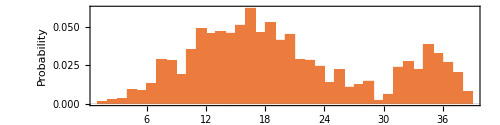

```mathematica
Histogram[scores,50,"Probability",Frame->True,FrameLabel->{"Years of Life Added Per Patient","Probability"},LabelStyle->{FontSize->18,FontColor->Black,FontFamily->"CMU Sans Serif"},PlotTheme->"Scientific",AspectRatio->1/4]
```

### Optimal Solution

```mathematica
T = Min[m, n];
var[i_,j_, t_] := Symbol["x"<>ToString@i<>"d" <>ToString@j <> "d" <> ToString@t];
waitConstr[w_, i_] :=  Table[Symbol["x"<>ToString@i<>"d" <>ToString@j <> "d" <> ToString@t] == 0, {j, m}, {t, w+1, T}] // Flatten;


obj1 = Table[-dis[[i,j]]*var[i,j,t], {i,  n}, {j,  m}, {t, T}] // Flatten // Total;
obj2 = Table[-w[[i]] * (1 - (Table[var[i,j,t], {j, m},{t, T}] // Flatten // Total )), {i, n}]  // Total;
obj = obj1 + obj2;
constr = Table[(Flatten[Table[var[i,j,t], {j, m},{t, T}] ] // Total) <= 1, {i, n}];
constr2 = Table[( Flatten[Table[var[i,j,t], {i, n}, {t, T}]] //Total) <= 1, {j, m}];
constr3 = Table[ (Flatten[Table[var[i,j,t], {i, n}, {j, m}]] //Total)<= 1, {t, T}];
constr4 = Table[var[i,j,t] >= 0, {i, n}, {j, m}, {t, T}] // Flatten;
constr5 = waitConstr[#[[1]], #[[2]]]&/@Transpose[{w, p}] // Flatten;
res = LinearOptimization[obj1+obj2, constr~Join~constr2~Join~constr3~Join~constr4~Join~constr5, Table[var[i,j,t]∈ Integers, {i, n}, {j, m}, {t, T}]//Flatten];


SplitRes[s_]:= ToString@s// StringSplit[#, "x"]& // StringSplit[#, "d"]& //ToExpression// Flatten;
ExtractAllocation[res_]:=SortBy[SplitRes[#[[1]]] & /@ Select[res, (#[[2]] == 1&)], Last];

ExtractAllocation[res]
-(obj/.res)/ n
```

{{1,5,1},{2,2,2},{5,1,4},{4,4,5}}

42.3179

Best Random

```mathematica
allocations[[Ordering[scores, -1][[1]]]]
```

{{2,5},{4,2},{3,4},{5,1}}

```mathematica
scores[[Ordering[scores, -1][[1]]]]
```

38.6712